```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/lamont/Dropbox/Colin_ControlTheory/HIV trapping code/BloomAntibodies

```mathematica
ablist ={"PGT121","VRC01","VRC34","PG9","PGT151","PGT145","10E8"};
```

```mathematica
ClearAll[mutvec]
```

```mathematica
mutvec[name_]:=Drop[Import[#],{1}]&@@FileNames[RegularExpression[".*"<>name<>".*meanmut.*"]]; 
sitevec[name_]:=Drop[Import[#],{1}]&@@FileNames[RegularExpression[".*"<>name<>".*meansite.*"]];
```

```mathematica
GetMutlist[name_]:= GetMutlist[name]=Module[{mvec,svec,mutlist},
mvec=mutvec[name];
svec=sitevec[name];
mutlist=Table[({#[[1,1]],
DeleteDuplicates[#[[;;,2]]],
DeleteDuplicates[#[[;;,3]]]
})&@Cases[mvec,{ii,a_,b_,c_/;Log[c]>-4}],{ii,svec[[;;5,1]]}];
Return[mutlist]
]
```

```mathematica
GenerateMutationSigniture[site_,muts_]:=Module[{present,wtout,mutout},
present=AAspresent[site];
mutout=Intersection[muts,present];
wtout=DeleteCases[Complement[present,muts],"*"];
If[Length[mutout]>0,
Return[{site,wtout,mutout}],
Return[Nothing]]
]
```

```mathematica
escaperules=Table[ab->(GenerateMutationSigniture[#[[1]],#[[3]]]&/@GetMutlist[ab]),{ab,ablist}]
```

{PGT121→{{334,{D,S},{G,N}},{332,{A,E,N,V},{D,I,K,T}},{330,{F,H,L,R,S,Y},{Q}}},VRC01→{{197,{D,N},{S}}},VRC34→{{88,{N},{K}},{90,{S,T},{A,E,K}},{85,{G,H},{A,C,D,E,F,I,K,L,N,P,Q,R,S,T,V,Y}},{524,{G,P},{A,E,R,S}},{512,{A},{G,T}}},PG9→{{160,{N},{K,Y}},{171,{K,P,R},{A,E,G,H,N,Q,S,T}},{169,{G,I,K,M,R,V,W},{E,L,T}},{162,{S,T},{A,I,P}}},PGT151→{{613,{S,T},{C,N}},{611,{G,N},{D,S}},{512,{A},{G,T}},{637,{D,N},{E,K,S,T}},{639,{T},{I,M}}},PGT145→{{166,{K,R},{A,E,G,S,T}},{160,{N},{K,Y}},{169,{G,I,K,L,T,V},{E,M,R,W}},{121,{K},{E}},{162,{S,T},{A,I,P}}},10E8→{{671,{K,N,S},{R,T}},{673,{F},{L,V}}}}

```mathematica
tab = Transpose[{{#[[1]],StringJoin/@#[[2;;3]]}&/@("PGT121"/.escaperules),
SiteEstimate@@@("PGT121"/.escaperules)}]
```

```mathematica
{NumberForm[#[[1]],{3,1}],NumberForm[#[[2]],{3,2}]}&/@SiteEstimate@@@("PGT121"/.escaperules)
```

{{77.0,{1.00,1.33}},{130.0,{1.09,1.19}},{67.4,{0.12,1.40}}}

```mathematica
MakeTable[name_]:=Module[{subtab,tab},
subtab={NumberForm[#[[1]],{3,1}],NumberForm[#,{3,2}]&/@#[[2]]}&/@SiteEstimate@@@(name/.escaperules);
tab = Transpose[{{#[[1]],StringJoin/@#[[2;;3]]}&/@(name/.escaperules),
subtab}];
Return[StringJoin[abrow[name],makeRow[titlerow],"\\hline",StringJoin[makeRow/@(Part[#,{1,3,2,4}]&/@Join@@@tab)]]]
]

makeRow[x_]:="
\\multirow{2}{4em}{"<>ToString[x[[1]]]<>"}
& \\multirow{2}{4em}{"<>ToString[x[[2]]]<>"}
&"<>ToString[x[[3,1]]]<>"
&"<>ToString[x[[4,1]]]<>"
\\\\
& 
& "<>ToString[x[[3,2]]]<>"& "<>ToString[x[[4,2]]]<>" \\\\
\\hline "

titlerow ={"Site","Fitness Cost $\\frac{\\delta}{\\mu}$",{"wt aa","mut aa"},{"$\\mu_{mut}$","$\\mu_{wt}$"}};
abrow[name_]:="\\multicolumn{4}{c}{ \\bf"<>ToString[name]<>"}\\\\ \\hline"
```

```mathematica
Export["tab.txt",StringJoin[MakeTable/@ablist]]
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

FindMaximum::nrnum: The function value Indeterminate is not a real number at {s} = {1045.73}.

ReplaceAll::reps: {s,200} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

General::stop: Further output of NumberForm::reqsigz will be suppressed during this calculation.

FindMaximum::nrnum: The function value Indeterminate is not a real number at {s} = {4116.56}.

tab.txt

```mathematica
Export["tab.txt",MakeTable[]]
```

tab.txt

```mathematica
ablist[[3]]/.escaperules
```

{{88,{N},{K}},{90,{S,T},{A,E,K}},{85,{G,H},{A,C,D,E,F,I,K,L,N,P,Q,R,S,T,V,Y}},{524,{G,P},{A,E,R,S}},{512,{A},{G,T}}}

```mathematica
{"K"}/.aaCodon
```

{{{A,A,A},{A,A,G}}}

```mathematica
{"N"}/.aaCodon
```

{{{A,A,T},{A,A,C}}}

```mathematica
startsites={"K"}
```

{K}

```mathematica
endsites={"N"}
```

{N}

```mathematica
OutCodons=Select[OutCodons,NearbyCodon[#1,InCodons]&]
```

```mathematica
OutCodons
```

{{A,A,T},{A,A,C}}

```mathematica
NearbyCodon[{"A","A","T"},InCodons]
```

False

```mathematica
InCodons
```

{{A,A,A},{A,A,G}}

```mathematica
SequenceOverlap[{"A","A","A"},{"A","A","T"}]
```

2

```mathematica
NearbyCodon[]
```

```mathematica
InCodons=Join@@(startsites/.aaCodon);
OutCodons=Join@@(endsites/.aaCodon);
```

```mathematica
OutCodons
```

{{A,A,T},{A,A,C}}

```mathematica
μνRates[8][{"N"},{"K"}]
```

{1/4,1/4}

```mathematica
ablist[[3]]/.escaperules
```

{{88,{N},{K}},{90,{S,T},{A,E,K}},{85,{G,H},{A,C,D,E,F,I,K,L,N,P,Q,R,S,T,V,Y}},{524,{G,P},{A,E,R,S}},{512,{A},{G,T}}}

```mathematica
f=TotalCountLikelihood[88,{"N"},{"K"}]
```

Function[s$,Total[Table[Mean[Table[If[Ne[patient,day]>0&&Total[WildtypeCounts[patient,day,88][{N},{K}]]>0,CountLikelihood[2 Ne[patient,day] s$,2 Ne[patient,day] cf$46525][WildtypeCounts[patient,day,88][{N},{K}]],0],{day,PatientDays[patient]}]],{patient,1,11}]]]

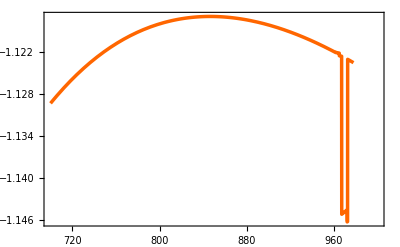

```mathematica
Plot[f[x],{x,700,1000}]
```

```mathematica
Apply[SiteEstimate,(ablist/.escaperules),{2}]
```

FindMaximum::nrnum: The function value Indeterminate is not a real number at {s} = {1045.73}.

ReplaceAll::reps: {s,200} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindMaximum::nrnum: The function value Indeterminate is not a real number at {s} = {4116.56}.

ReplaceAll::reps: {s,200} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{{55.2898,{1.,2.}},{130.026,{1.09266,1.192}},{67.4091,{0.116333,1.39599}}},{{1396.62,{0.5,1.}}},{{s/.{s,200},{0.263996,0.263996}},{1446.52,{0.479199,0.798665}},{-125.9,{2.57199,0.482249}},{78.4173,{1.514,0.672887}},{1351.68,{1.132,0.565999}}},{{208.501,{0.395995,0.197997}},{157.095,{1.352,0.623998}},{421.099,{0.525522,0.919663}},{707.023,{1.232,1.12}}},{{2128.2,{0.279199,0.697997}},{933.744,{1.33333,2.}},{1351.68,{1.132,0.565999}},{182.383,{0.829995,0.414998}},{s/.{s,200},{1.,1.}}},{{98.3379,{0.730997,0.584797}},{208.501,{0.395995,0.197997}},{67.0807,{0.593042,1.364}},{83.286,{1.,1.}},{707.023,{1.232,1.12}}},{{87.4604,{0.411197,0.513996}},{266.275,{1.39599,0.465332}}}}

```mathematica
μνRates
```

```mathematica
StringJoin[makeRow[{"Site","Fitness Cost $\\frac{Δ}{μ}$",{"wt aa","mut aa"},{"$μ_{mut}$","$μ_{wt}$"}}]]
```

\multirow{2}{4em}{Site}
& \multirow{2}{4em}{Fitness Cost $\frac{Δ}{μ}$}
&wt aa
&$μ_{mut}$
\\
& 
& mut aa& $μ_{wt}$ \\
\hline

```mathematica
StringJoin@@makeRow/@xx
```

\multirow{2}{4em}{166}
& \multirow{2}{4em}{140.0}
&KR
&0.73
\\
& 
& AEGST& 0.29 \\
\hline
\multirow{2}{4em}{160}
& \multirow{2}{4em}{150.0}
&N
&0.13
\\
& 
& KY& 0.13 \\
\hline
\multirow{2}{4em}{169}
& \multirow{2}{4em}{67.1}
&GIKLTV
&0.59
\\
& 
& EMRW& 1.36 \\
\hline
\multirow{2}{4em}{121}
& \multirow{2}{4em}{83.3}
&K
&1.00
\\
& 
& E& 1.00 \\
\hline
\multirow{2}{4em}{162}
& \multirow{2}{4em}{707.0}
&ST
&1.23
\\
& 
& AIP& 1.12 \\
\hline

```mathematica
"\\"
```

\

```mathematica
?Round
```

```mathematica
TableForm[Join@@@tab]
```

334 | DS
GN | 76.9622 | 1.
1.33333
332 | AENV
DIKT | 130.026 | 1.09266
1.192
330 | FHLRSY
Q | 67.4091 | 0.116333
1.39599

```mathematica
SiteEstimate@@@("VRC01"/.escaperules)
```

{{1624.38,{0.5,0.5}}}

```mathematica
SiteEstimate@@@("VRC34"/.escaperules)
```

Dot::dotsh: Tensors {{{0},{Mean[{}]}}} and {1,0.131998} have incompatible shapes.

FindMaximum::nrnum: The function value «1» is not a real number at {s} = {200.}.

ReplaceAll::reps: {s,200} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Dot::dotsh: Tensors {{{0},{Mean[{}]}}} and {1,0.131998} have incompatible shapes.

{{s/.{s,200},{{{0},{Mean[{}]}}}.{1,0.131998}},{1539.41,{0.479199,0.598999}},{-86.6532,{2.57199,0.291169}},{78.4173,{1.514,0.672887}},{1351.68,{1.132,0.565999}}}

```mathematica
GetSigniture[ablist[[5]]]
```

{{613,{S},{Y,D,L,V,K,I,Q,M,C,A,R,N,G,E,H,F,W}},{611,{N},{S,R,K,M,A,Y,I,H,Q,E,L,C,V,D,F,T}},{512,{A},{L,E,Y,Q,W,T,M,H,I,V,N,S,G}},{637,{N},{R,Q,S,G,T,A,K,V,F,W,H,M,E}},{639,{T},{A,K,R,Y,V,M,I,Q}}}

```mathematica
Getsigniture[ablist[[1]]]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression 6222+3 {}⟦1,1⟧ cannot be used as a part specification.

Part::pkspec1: The expression {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,«9669»}⟦6222+3 {}⟦1,1⟧⟧ cannot be used as a part specification.

Part::pkspec1: The expression 6223+3 {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

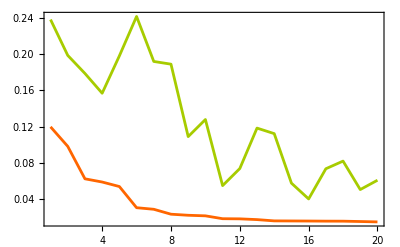

```mathematica
ListPlot[{sitevec[[;;20,2]],sitevec[[;;20,3]]},PlotRange->All,Joined->True]
```

```mathematica
sitevec[[;;10,1]]
```

{166,160,169,121,162,124,127,202,315,123}

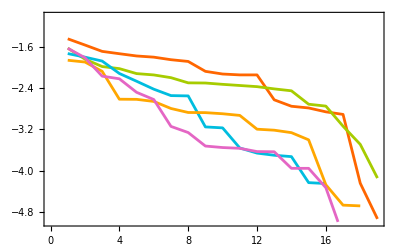

```mathematica
ListPlot[Log@Table[Cases[mutvec,{ii,___}][[;;,4]],{ii,sitevec[[;;5,1]]}],Joined->True,PlotRange->{-5,-1}]
```

```mathematica
mutlistpg145=Table[({#[[1,1]],
DeleteDuplicates[#[[;;,2]]],
DeleteDuplicates[#[[;;,3]]]
})&@Cases[mutvec,{ii,a_,b_,c_/;Log[c]>-2.5}],{ii,sitevec[[;;5,1]]}]
```

{{166,{R},{M,V,A,S,L,Q,N,T,G,Y,F,I}},{160,{N},{D,I,L,V,E,W,T,M,Q,F,P,Y,C,S}},{169,{K},{E,F,D,Y,N,W}},{121,{K},{E,Q,L}},{162,{T},{P,R,A,E,N}}}

{166,160,169,121,162}

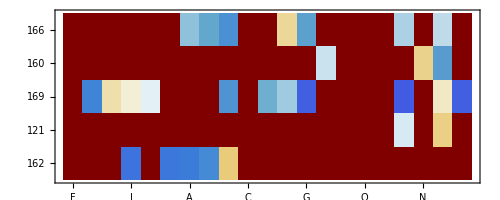

```mathematica
MatrixPlot[Table[Log@Total[Mean/@Table[SNPAAfreq[pat,day,site],{pat,11},{day,PatientDays[pat]}]],{site,mutlistpg145[[;;,1]]}],FrameTicks->{{Transpose@{Range[Length[#]],#}&@mutlistpg145[[;;,1]],None},{Transpose@{Range[Length[AAs]],AAs},None}}]
```

```mathematica
ObservedFreq[site_,wt_,muts_]:=Module[{wtfreq,mutfreq},
wtfreq=Mean[Mean/@Table[wt/.SNPAArule[ii,day,site],{ii,1,11},{day,PatientDays[ii]}]];
mutfreq=Mean[Mean/@Table[muts/.SNPAArule[ii,day,site],{ii,1,11},{day,PatientDays[ii]}]];
{Total[wtfreq],Total[mutfreq]}
]
```

```mathematica
GenerateMutationSigniture[#[[1]],#[[3]]]&/@mutlistpg145
```

{{166,{E,K,R},{A,G,S,T}},{160,{K,N},{Y}},{169,{*,G,I,K,L,M,R,T,V},{E,W}},{121,{K},{E}},{162,{I,S,T},{A,P}}}

```mathematica
ObservedFreq[169,{"*","G","I","K","L","M","R","T","V"},{"E","W"}]
```

{0.771642,0.0180947}

```mathematica
SNPAArule[2,PatientDays[2][[4]],169]
```

{F→0.,L→0.,V→1.,I→0.,M→0.,P→0.,A→0.,S→0.,T→0.,C→0.,W→0.,R→0.,G→0.,Y→0.,H→0.,Q→0.,D→0.,E→0.,N→0.,K→0.,*→0.}

```mathematica
mutlistpg145
```

{{166,{R},{M,V,A,S,L,Q,N,T,G,Y,F,I,E,H,W,P,C}},{160,{N},{D,I,L,V,E,W,T,M,Q,F,P,Y,C,S,R,K}},{169,{K},{E,F,D,Y,N,W,H,S}},{121,{K},{E,Q,L,C,S,P,V,T,I,H,A}},{162,{T},{P,R,A,E,N,Y}}}